# Dirac Delta

info@cafeplanck.com

```mathematica
DiracDelta[x]//TraditionalForm
```

x

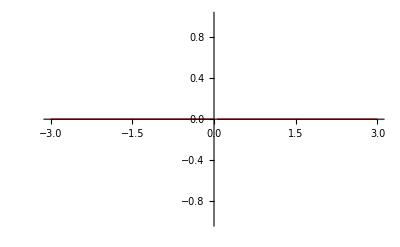

```mathematica
Plot[DiracDelta[x],{x,-3,3},PlotStyle->{Red,Thick}]
```

```mathematica
0
```

DiracDelta[0]

```mathematica
∫_(-∞)^(+∞) x Cos[x]ⅆx
```

1

```mathematica
∫_(-∞)^(+∞) x-2 f[x]ⅆx
```

f[2]

```mathematica
Integrate[DiracDelta[x-a] f[x],{x,-∞,∞},Assumptions->a∈Reals]
```

f[a]

```mathematica
∫x ⅆx
```

HeavisideTheta[x]

```mathematica
FourierTransform[DiracDelta[y],y,x]
```

1/(√(2 π))

```mathematica
LaplaceTransform[DiracDelta[x],x,s]
```

1